0.906215-ⅇ^(-0.463794-1.01913 x)

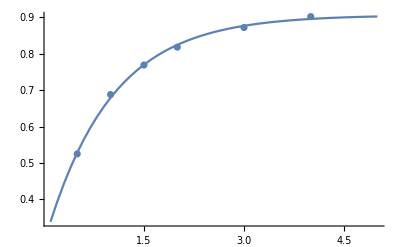

{0.528404,0.679242,0.824299,0.876651,0.895545}

{1.00648,0.987271,1.07191,1.0717,0.992843}

```mathematica
data={{0.5,0.525},{1,0.688},{1.5,0.769},{2,0.818},{3,0.872},{4,0.902}};
nlm=NonlinearModelFit[data,c-Exp[b-x*a],{a,b,c},x];
Normal[nlm]
Show[ListPlot[data],Plot[nlm[x],{x,0.1,5},PlotRange->All],PlotRange->All]
{nlm[.5],nlm[1],nlm[2],nlm[3],nlm[4]}
{nlm[.5]/.525,nlm[1]/.688,nlm[2]/.769,nlm[3]/.818,nlm[4]/.902}
```

```mathematica
k[k_]:=0.9-Exp[-0.5- k];
{k[.5],k[1],k[1.5],k[2],k[3],k[4]}
{k[.5]/.525,k[1]/.688,k[1.5]/.769,k[2]/.818,k[3]/.872,k[4]/.902}
```

{0.532121,0.67687,0.764665,0.817915,0.869803,0.888891}

{1.01356,0.983822,0.994362,0.999896,0.99748,0.985467}

```mathematica
k[k_]:=0.9-Exp[-0.5- k];
L[d_,l_,N_]:=k[l/d]*π^2*10^-7*N^2*d^2/l;
NN=222;
L[0.380,0.72*NN,NN]
```

0.0000395485